```mathematica
r[x, t] = t / x
```

t/x

```mathematica
h[x, t] = f[r[x, t]]
```

f[t/x]

```mathematica
D[h[x, t], x]
```

-(t f')/x^2

```mathematica
G[x, t] = x g[r[x, t]]
```

x g[t/x]

```mathematica
ode1 = D[h[x, t], t] + h[x, t]^2 D[h[x, t], x] - D[G[x, t], x] D[h[x, t], x] h[x, t] - h[x, t]^2/2 D[G[x, t], x,x] == 0 // FullSimplify
```

(2 f' (x^2-t f[t/x] (x f[t/x]-x g[t/x]+t g'))-t^2 f[t/x]^2 g'')/x==0

```mathematica
ode2 = D[G[x, t], t] + h[x, t]^2/2 D[G[x, t], x] - h[x, t] D[G[x, t], x]^2 + G[x, t] h[x, t] D[h[x, t], x] - G[x, t] D[G[x, t], x] D[h[x, t], x] - G[x, t] h[x, t] D[G[x, t], x, x] == 0 // FullSimplify
```

1/x(-2 t x g[t/x]^2 f'-2 (x^2-t^2 g[t/x] f') g'+x f[t/x]^2 (-x g[t/x]+t g')+2 f[t/x] (x^2 g[t/x]^2+t^2 g'^2+t g[t/x] (x f'-2 x g'+t g'')))==0

```mathematica
ClearAll[x, t, f, g, r]
```

```mathematica
r
```

r

```mathematica
eqn1 = 2 f[r]^3 - 2 D[f[r], r] + 18 r^2 f[r] D[f[r], r] D[g[r], r] + 3 r f[r]^2 (2 (D[f[r], r] + 3 D[g[r], r])+ 3 r D[g[r], r, r]) == 0
```

2 f[r]^3-2 f'+18 r^2 f[r] f' g'+3 r f[r]^2 (2 (f'+3 g')+3 r g'')==0

```mathematica
eqn2 = -2 (1 - 9 r^2 g[r] D[f[r], r]) D[g[r], r] + f[r]^2 (2 g[r] + 3 r D[g[r], r]) + 6 r f[r] (3 r D[g[r], r]^2 + g[r] (D[f[r], r] + 5 D[g[r], r]) + 3 r D[g[r], r, r]) == 0
```

-2 (1-9 r^2 g[r] f') g'+f[r]^2 (2 g[r]+3 r g')+6 r f[r] (3 r g'^2+g[r] (f'+5 g')+3 r g'')==0

```mathematica
<< Sym`
```

Loading Package Sym...

Set::wrsym: Symbol $Percent is Protected.

Set::write: Tag ClassicalSymmetries in Options[ClassicalSymmetries] is Protected.

Set::write: Tag CharacteristicDeq in Options[CharacteristicDeq] is Protected.

Set::write: Tag CharacterizeEq in Options[CharacterizeEq] is Protected.

General::stop: Further output of Set::write will be suppressed during this calculation.

GUIKit`GUILoad::nffil: File not found during GUIKit`GUILoad[AbortDialog].

SetDelayed::write: Tag AbelianElement in AbelianElement[structureconstants_,SubAlgebra_List:{}]/;ArrayQ[structureconstants,3] is Protected.

SetDelayed::write: Tag AbelianQ in AbelianQ[structureconstants_,SubAlgebra_List,SubAlgebraIndex_List:{}]/;ArrayQ[structureconstants,3] is Protected.

SetDelayed::write: Tag AddDiscreteFunction in AddDiscreteFunction[fun_?AtomQ]/;Context[fun]===Global` is Protected.

General::stop: Further output of SetDelayed::write will be suppressed during this calculation.

Set::wrsym: Symbol TOF is Protected.

Package Loaded
version 1.92 for Mathematica v6.x (Last update: 06/01/2009)

```mathematica
symm = ClassicalSymmetries[{eqn1, eqn2}]
```

First::nofirst: {} has zero length and no first element.

First::normal: Nonatomic expression expected at position 1 in First[True].

invhint::Invalid hint detected

{}

```mathematica
{}
ClearAll[f, g, r, t]
```

{}

```mathematica
sol = DSolve[{f'[t]== 9/8 f[t]^2 - f[t]^3/2, g'[t]== 15/4 f[t] g[t] - 5/4 f[t]^2 g[t]}, {f, g}, t]
```

{{f→Function[{t},InverseFunction[4/81 Log[9-4 #1]-(4 Log[#1])/81+1/(9 #1)&][-t/8+C[1]]],g→Function[{t},(C[2] (InverseFunction[4/81 Log[9-4 #1]-(4 Log[#1])/81+1/(9 #1)&][-t/8+C[1]])^(10/3) (-9+4 InverseFunction[4/81 Log[9-4 #1]-(4 Log[#1])/81+1/(9 #1)&][-t/8+C[1]])^(5/2))/(9-4 InverseFunction[4/81 Log[9-4 #1]-(4 Log[#1])/81+1/(9 #1)&][-t/8+C[1]])^(10/3)]}}

```mathematica
ClearAll[f, g, r, t]
```

```mathematica
symm = ClassicalSymmetries[{f'[t]== 9/8 f[t]^2 - f[t]^3/2, g'[t]== 15/4 f[t] g[t] - 5/4 f[t]^2 g[t]}, Verbose-> True]
```

{{{(((120 f η_2[t,f,g])/((-3+2 f) g)-(40 f^2 η_2[t,f,g])/((-3+2 f) g)-(120 f η_2_(, g))/(-3+2 f)+(40 f^2 η_2_(, g))/(-3+2 f)+(450 f^2 g ξ_(, g))/(-3+2 f)-(300 f^3 g ξ_(, g))/(-3+2 f)+(50 f^4 g ξ_(, g))/(-3+2 f)-(36 f^2 η_2_(, f))/((-3+2 f) g)+(16 f^3 η_2_(, f))/((-3+2 f) g)+(135 f^3 ξ_(, f))/(-3+2 f)-(105 f^4 ξ_(, f))/(-3+2 f)+(20 f^5 ξ_(, f))/(-3+2 f)-(32 η_2_(, t))/((-3+2 f) g)+(120 f ξ_(, t))/(-3+2 f)-(40 f^2 ξ_(, t))/(-3+2 f)) ∂_f #1+(-(120 η_2[t,f,g])/(-3+2 f)+(80 f η_2[t,f,g])/(-3+2 f)) ∂_g #1)+(-(120 ξ[t,f,g])/(-3+2 f)+(80 f ξ[t,f,g])/(-3+2 f)) ∂_t #1&,{-14040 f^2 η_2[t,f,g]+21600 f^3 η_2[t,f,g]-10080 f^4 η_2[t,f,g]+1440 f^5 η_2[t,f,g]+14040 f^2 g η_2_(, g)-21600 f^3 g η_2_(, g)+10080 f^4 g η_2_(, g)-1440 f^5 g η_2_(, g)+52650 f^3 g^2 ξ_(, g)-87750 f^4 g^2 ξ_(, g)+55800 f^5 g^2 ξ_(, g)-16200 f^6 g^2 ξ_(, g)+1800 f^7 g^2 ξ_(, g)-10800 f^2 g^2 η_2_(, gg)+14400 f^3 g^2 η_2_(, gg)-6000 f^4 g^2 η_2_(, gg)+800 f^5 g^2 η_2_(, gg)+40500 f^3 g^3 ξ_(, gg)-67500 f^4 g^3 ξ_(, gg)+40500 f^5 g^3 ξ_(, gg)-10500 f^6 g^3 ξ_(, gg)+1000 f^7 g^3 ξ_(, gg)+6480 f^3 η_2_(, f)-10008 f^4 η_2_(, f)+4896 f^5 η_2_(, f)-768 f^6 η_2_(, f)+7290 f^4 g ξ_(, f)-13770 f^5 g ξ_(, f)+10350 f^6 g ξ_(, f)-3600 f^7 g ξ_(, f)+480 f^8 g ξ_(, f)-6480 f^3 g η_2_(, fg)+9360 f^4 g η_2_(, fg)-4320 f^5 g η_2_(, fg)+640 f^6 g η_2_(, fg)+24300 f^4 g^2 ξ_(, fg)-43200 f^5 g^2 ξ_(, fg)+27900 f^6 g^2 ξ_(, fg)-7800 f^7 g^2 ξ_(, fg)+800 f^8 g^2 ξ_(, fg)-972 f^4 η_2_(, ff)+1512 f^5 η_2_(, ff)-768 f^6 η_2_(, ff)+128 f^7 η_2_(, ff)+3645 f^5 g ξ_(, ff)-6885 f^6 g ξ_(, ff)+4770 f^7 g ξ_(, ff)-1440 f^8 g ξ_(, ff)+160 f^9 g ξ_(, ff)+7488 f η_2_(, t)-8640 f^2 η_2_(, t)+2304 f^3 η_2_(, t)+1440 f^3 g ξ_(, t)-720 f^4 g ξ_(, t)-5760 f g η_2_(, tg)+5760 f^2 g η_2_(, tg)-1280 f^3 g η_2_(, tg)+21600 f^2 g^2 ξ_(, tg)-28800 f^3 g^2 ξ_(, tg)+12000 f^4 g^2 ξ_(, tg)-1600 f^5 g^2 ξ_(, tg)-1728 f^2 η_2_(, tf)+1920 f^3 η_2_(, tf)-512 f^4 η_2_(, tf)+6480 f^3 g ξ_(, tf)-9360 f^4 g ξ_(, tf)+4320 f^5 g ξ_(, tf)-640 f^6 g ξ_(, tf)-768 η_2_(, tt)+512 f η_2_(, tt)+2880 f g ξ_(, tt)-2880 f^2 g ξ_(, tt)+640 f^3 g ξ_(, tt)==0}},(-3+2 f) g≠0}}

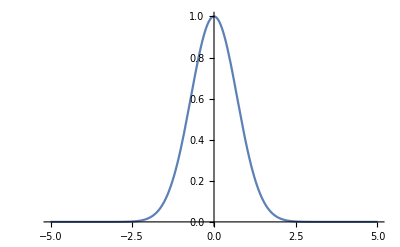

```mathematica
Plot[Exp[-x^2], {x, -5, 5}]
```

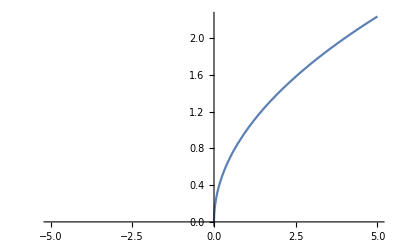

```mathematica
Plot[Sqrt[x], {x, -5, 5}]
```

```mathematica
E[x^2]
```

ⅇ[x^2]